This notebook is to study the effect of J on the length distribution for kinetic+rotation+vibration energy.

```mathematica
Clear[vibration]
∑_(n=1)^l Exp[vibration*x*Cos[Pi*n/(2l)]]
```

∑_(n=1)^l ⅇ^(vibration x Cos[(n π)/(2 l)])

```mathematica
A=1
gamma = 1.5
vibration = 1
Timing[Jkrj=Table[u/.FindRoot[A×x^-3×ⅇ^(-J×x)×(ⅇ^-u+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-u×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))-1,{u,-3},MaxIterations->10000],{J,0.5,3.5,0.5},{x,0.01,15,0.1}]]
```

1

1.5

1

General::munfl: 175.883/(20392982741189116246929760449986148747075145648674235982781068340853993944677551349687«139»005154182397262875200268932124981878786621440000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (176.876 89)/(31407209806241603786822089316483836240259480043696619292995749440436493541620430903821«143»817707435274785196699124005923162587377172480000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (177.87 32041)/(19679129520394864100746984723922442111421785005779427716605276684388698123308529595716«148»912479447490854773711963133521399878873251840000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{18444.6,{{13.8105,6.58283,4.68128,3.64585,3.00253,2.56478,2.24285,1.99147,1.78631,1.61336,1.46397,1.33252,1.21515,1.10914,1.01247,0.923635,0.841452,0.765001,0.693539,0.626461,0.563268,0.50354,0.446926,0.393124,0.341875,0.292954,0.246165,0.201336,0.158314,0.116964,0.0771654,0.03881,0.00180007,-0.0339523,-0.0685271,-0.101997,-0.134428,-0.165882,-0.196413,-0.226073,-0.254909,-0.282966,-0.310282,-0.336896,-0.362842,-0.388153,-0.412859,-0.436987,-0.460565,-0.483617,-0.506165,-0.528232,-0.549838,-0.571001,-0.591741,-0.612073,-0.632013,-0.651578,-0.67078,-0.689634,-0.708152,-0.726347,-0.744229,-0.76181,-0.7791,-0.796108,-0.812845,-0.829318,-0.845537,-0.86151,-0.877243,-0.892745,-0.908022,-0.923082,-0.93793,-0.952572,-0.967015,-0.981265,-0.995325,-1.0092,-1.0229,-1.03643,-1.04978,-1.06297,-1.076,-1.08888,-1.1016,-1.11417,-1.1266,-1.13888,-1.15103,-1.16304,-1.17492,-1.18667,-1.19829,-1.2098,-1.22117,-1.23244,-1.24358,-1.25462,-1.26554,-1.27635,-1.28706,-1.29766,-1.30816,-1.31856,-1.32887,-1.33907,-1.34919,-1.35921,-1.36914,-1.37898,-1.38873,-1.3984,-1.40798,-1.41748,-1.4269,-1.43624,-1.4455,-1.45468,-1.46379,-1.47282,-1.48178,-1.49067,-1.49949,-1.50824,-1.51692,-1.52553,-1.53407,-1.54255,-1.55097,-1.55932,-1.56761,-1.57583,-1.584,-1.59211,-1.60016,-1.60815,-1.61608,-1.62396,-1.63178,-1.63955,-1.64727,-1.65493,-1.66254,-1.67009,-1.6776,-1.68505,-1.69246,-1.69982},{13.8055,6.52872,4.5867,3.52726,2.87142,2.425,2.095,1.83533,1.62162,1.43994,1.28175,1.14151,1.01543,0.900819,0.795691,0.698549,0.608233,0.523823,0.44458,0.369899,0.299279,0.2323,0.168604,0.107887,0.0498844,-0.00563177,-0.0588627,-0.109985,-0.159156,-0.206516,-0.252189,-0.296288,-0.338915,-0.380161,-0.420111,-0.458841,-0.496421,-0.532915,-0.568382,-0.602876,-0.636448,-0.669144,-0.701007,-0.732078,-0.762394,-0.791989,-0.820896,-0.849146,-0.876767,-0.903785,-0.930227,-0.956114,-0.98147,-1.00632,-1.03067,-1.05455,-1.07798,-1.10097,-1.12354,-1.1457,-1.16747,-1.18885,-1.20988,-1.23054,-1.25086,-1.27086,-1.29052,-1.30988,-1.32894,-1.3477,-1.36618,-1.38438,-1.40231,-1.41999,-1.43741,-1.45458,-1.47152,-1.48822,-1.5047,-1.52095,-1.53699,-1.55282,-1.56845,-1.58387,-1.5991,-1.61415,-1.629,-1.64368,-1.65818,-1.67251,-1.68667,-1.70066,-1.7145,-1.72817,-1.7417,-1.75507,-1.76829,-1.78137,-1.79431,-1.80711,-1.81978,-1.83231,-1.84471,-1.85699,-1.86914,-1.88116,-1.89307,-1.90486,-1.91653,-1.92809,-1.93954,-1.95088,-1.96211,-1.97324,-1.98426,-1.99518,-2.00601,-2.01673,-2.02735,-2.03789,-2.04833,-2.05867,-2.06893,-2.0791,-2.08918,-2.09917,-2.10909,-2.11891,-2.12866,-2.13833,-2.14791,-2.15742,-2.16686,-2.17621,-2.1855,-2.19471,-2.20384,-2.21291,-2.22191,-2.23083,-2.23969,-2.24849,-2.25721,-2.26587,-2.27447,-2.28301,-2.29148,-2.29989,-2.30824,-2.31653},{13.8005,6.47466,4.49304,3.412,2.74601,2.29251,1.9555,1.68838,1.46689,1.27726,1.1111,0.96296,0.829119,0.706926,0.594426,0.490135,0.3929,0.301804,0.216108,0.135201,0.0585789,-0.0141866,-0.0834586,-0.14955,-0.212732,-0.27324,-0.331284,-0.387048,-0.440696,-0.492374,-0.542215,-0.590337,-0.636849,-0.681848,-0.725423,-0.767657,-0.808625,-0.848395,-0.887031,-0.924592,-0.961132,-0.996703,-1.03135,-1.06512,-1.09805,-1.13017,-1.16154,-1.19217,-1.2221,-1.25136,-1.27997,-1.30797,-1.33538,-1.36221,-1.3885,-1.41426,-1.43951,-1.46428,-1.48857,-1.51241,-1.5358,-1.55878,-1.58134,-1.6035,-1.62529,-1.6467,-1.66775,-1.68845,-1.70882,-1.72886,-1.74858,-1.76799,-1.7871,-1.80593,-1.82447,-1.84273,-1.86073,-1.87847,-1.89596,-1.9132,-1.9302,-1.94697,-1.96351,-1.97982,-1.99593,-2.01182,-2.0275,-2.04299,-2.05828,-2.07337,-2.08829,-2.10301,-2.11756,-2.13194,-2.14615,-2.16019,-2.17406,-2.18778,-2.20134,-2.21475,-2.22801,-2.24112,-2.25409,-2.26691,-2.2796,-2.29216,-2.30458,-2.31688,-2.32904,-2.34109,-2.35301,-2.36481,-2.37649,-2.38806,-2.39951,-2.41086,-2.42209,-2.43322,-2.44424,-2.45515,-2.46597,-2.47669,-2.4873,-2.49783,-2.50825,-2.51859,-2.52883,-2.53898,-2.54905,-2.55902,-2.56891,-2.57872,-2.58844,-2.59808,-2.60764,-2.61713,-2.62653,-2.63586,-2.64511,-2.65429,-2.66339,-2.67242,-2.68138,-2.69027,-2.6991,-2.70785,-2.71654,-2.72516,-2.73371,-2.74221},{13.7955,6.42065,4.40038,3.30012,2.62606,2.16668,1.8234,1.54943,1.32073,1.12378,0.950336,0.795058,0.65429,0.525419,0.406513,0.296097,0.193018,0.0963583,0.00536869,-0.0805681,-0.161969,-0.239273,-0.312854,-0.383037,-0.450105,-0.514304,-0.575854,-0.63495,-0.691765,-0.746456,-0.799162,-0.85001,-0.899118,-0.946589,-0.99252,-1.037,-1.08011,-1.12192,-1.1625,-1.20192,-1.24024,-1.27751,-1.31377,-1.34909,-1.3835,-1.41704,-1.44976,-1.48169,-1.51286,-1.54331,-1.57306,-1.60215,-1.6306,-1.65844,-1.68569,-1.71237,-1.7385,-1.76411,-1.78922,-1.81383,-1.83798,-1.86166,-1.88492,-1.90774,-1.93016,-1.95218,-1.97381,-1.99508,-2.01598,-2.03654,-2.05676,-2.07665,-2.09622,-2.11548,-2.13444,-2.15312,-2.17151,-2.18962,-2.20746,-2.22505,-2.24238,-2.25947,-2.27631,-2.29293,-2.30931,-2.32547,-2.34142,-2.35715,-2.37268,-2.388,-2.40314,-2.41807,-2.43283,-2.4474,-2.46179,-2.476,-2.49005,-2.50393,-2.51765,-2.5312,-2.5446,-2.55785,-2.57095,-2.5839,-2.59671,-2.60938,-2.62191,-2.63431,-2.64657,-2.65871,-2.67072,-2.6826,-2.69436,-2.70601,-2.71753,-2.72894,-2.74024,-2.75143,-2.7625,-2.77347,-2.78434,-2.7951,-2.80576,-2.81633,-2.82679,-2.83716,-2.84743,-2.85762,-2.86771,-2.87771,-2.88762,-2.89745,-2.90719,-2.91684,-2.92642,-2.93591,-2.94533,-2.95466,-2.96392,-2.9731,-2.98221,-2.99124,-3.0002,-3.00909,-3.01791,-3.02666,-3.03534,-3.04395,-3.0525,-3.06098},{13.7905,6.3667,4.30876,3.19165,2.5113,2.04692,1.69787,1.41748,1.18205,0.978303,0.798189,0.636465,0.489535,0.354816,0.230387,0.114775,0.00682179,-0.0944048,-0.189667,-0.279597,-0.364728,-0.445516,-0.522351,-0.595572,-0.665477,-0.732327,-0.796353,-0.857763,-0.916742,-0.973455,-1.02805,-1.08067,-1.13144,-1.18046,-1.22785,-1.27369,-1.31807,-1.36108,-1.40279,-1.44326,-1.48257,-1.52076,-1.5579,-1.59403,-1.6292,-1.66347,-1.69686,-1.72942,-1.76118,-1.79219,-1.82246,-1.85204,-1.88095,-1.90922,-1.93687,-1.96393,-1.99042,-2.01636,-2.04177,-2.06667,-2.09108,-2.11502,-2.13851,-2.16155,-2.18417,-2.20638,-2.22819,-2.24961,-2.27067,-2.29136,-2.3117,-2.3317,-2.35138,-2.37074,-2.38979,-2.40854,-2.42699,-2.44517,-2.46307,-2.4807,-2.49808,-2.5152,-2.53207,-2.54871,-2.56511,-2.58128,-2.59723,-2.61297,-2.6285,-2.64382,-2.65894,-2.67387,-2.6886,-2.70315,-2.71752,-2.73171,-2.74573,-2.75957,-2.77325,-2.78677,-2.80014,-2.81334,-2.8264,-2.8393,-2.85206,-2.86468,-2.87716,-2.88951,-2.90172,-2.9138,-2.92575,-2.93757,-2.94928,-2.96086,-2.97232,-2.98367,-2.9949,-3.00602,-3.01704,-3.02794,-3.03874,-3.04943,-3.06003,-3.07052,-3.08092,-3.09121,-3.10142,-3.11153,-3.12155,-3.13148,-3.14132,-3.15107,-3.16074,-3.17032,-3.17982,-3.18924,-3.19858,-3.20784,-3.21703,-3.22613,-3.23517,-3.24412,-3.25301,-3.26182,-3.27057,-3.27924,-3.28785,-3.29638,-3.30486,-3.31326},{13.7855,6.3128,4.21824,3.08659,2.40142,1.93264,1.57819,1.29171,1.04994,0.839892,0.653684,0.486168,0.333794,0.193999,0.0648635,-0.0550969,-0.167057,-0.271968,-0.370613,-0.463646,-0.551623,-0.635018,-0.714241,-0.78965,-0.861558,-0.930242,-0.995948,-1.0589,-1.11928,-1.17728,-1.23306,-1.28676,-1.33852,-1.38844,-1.43665,-1.48325,-1.52832,-1.57196,-1.61424,-1.65523,-1.69501,-1.73363,-1.77115,-1.80764,-1.84313,-1.87768,-1.91133,-1.94411,-1.97608,-2.00727,-2.0377,-2.06742,-2.09645,-2.12482,-2.15255,-2.17968,-2.20623,-2.23221,-2.25765,-2.28258,-2.307,-2.33094,-2.35442,-2.37745,-2.40004,-2.42222,-2.44399,-2.46537,-2.48637,-2.50701,-2.52729,-2.54723,-2.56684,-2.58612,-2.60509,-2.62376,-2.64214,-2.66023,-2.67804,-2.69558,-2.71286,-2.72988,-2.74666,-2.76319,-2.77949,-2.79557,-2.81142,-2.82705,-2.84247,-2.85768,-2.8727,-2.88751,-2.90214,-2.91658,-2.93084,-2.94492,-2.95882,-2.97256,-2.98613,-2.99954,-3.01278,-3.02588,-3.03882,-3.05162,-3.06427,-3.07677,-3.08914,-3.10137,-3.11347,-3.12544,-3.13728,-3.149,-3.16059,-3.17206,-3.18341,-3.19465,-3.20578,-3.21679,-3.22769,-3.23849,-3.24918,-3.25977,-3.27026,-3.28064,-3.29093,-3.30113,-3.31123,-3.32123,-3.33115,-3.34098,-3.35071,-3.36037,-3.36993,-3.37942,-3.38882,-3.39814,-3.40738,-3.41654,-3.42563,-3.43464,-3.44357,-3.45244,-3.46123,-3.46994,-3.47859,-3.48717,-3.49569,-3.50413,-3.51251,-3.52083},{13.7805,6.25896,4.1289,2.98492,2.29608,1.82334,1.46371,1.17143,0.923692,0.707814,0.516066,0.343382,0.186245,0.0420946,-0.0910004,-0.214545,-0.32974,-0.437565,-0.538829,-0.634214,-0.7243,-0.809584,-0.890498,-0.967418,-1.04068,-1.11056,-1.17734,-1.24124,-1.30248,-1.36123,-1.41767,-1.47196,-1.52422,-1.5746,-1.6232,-1.67013,-1.7155,-1.75938,-1.80187,-1.84304,-1.88295,-1.92169,-1.9593,-1.99584,-2.03137,-2.06594,-2.09959,-2.13236,-2.1643,-2.19544,-2.22582,-2.25547,-2.28443,-2.31271,-2.34035,-2.36738,-2.39382,-2.41969,-2.44501,-2.46982,-2.49411,-2.51792,-2.54126,-2.56415,-2.5866,-2.60864,-2.63026,-2.6515,-2.67235,-2.69284,-2.71297,-2.73276,-2.75221,-2.77134,-2.79016,-2.80868,-2.8269,-2.84483,-2.86249,-2.87988,-2.897,-2.91387,-2.9305,-2.94688,-2.96303,-2.97895,-2.99465,-3.01013,-3.0254,-3.04047,-3.05533,-3.07001,-3.08449,-3.09878,-3.11289,-3.12683,-3.1406,-3.15419,-3.16762,-3.18089,-3.194,-3.20696,-3.21977,-3.23243,-3.24494,-3.25732,-3.26955,-3.28165,-3.29362,-3.30546,-3.31718,-3.32877,-3.34023,-3.35158,-3.36281,-3.37393,-3.38493,-3.39582,-3.40661,-3.41729,-3.42786,-3.43833,-3.44871,-3.45898,-3.46915,-3.47924,-3.48922,-3.49912,-3.50893,-3.51865,-3.52828,-3.53782,-3.54728,-3.55666,-3.56596,-3.57518,-3.58432,-3.59338,-3.60236,-3.61127,-3.62011,-3.62888,-3.63757,-3.64619,-3.65475,-3.66323,-3.67165,-3.68,-3.68829,-3.69652}}}

```mathematica
J05 = Jkrj[[1]]
J1 = Jkrj[[2]]
J105 = Jkrj[[3]]
J2 = Jkrj[[4]]
J205=Jkrj[[5]]
J3 = Jkrj[[6]]
J305= Jkrj[[7]]
```

{13.8105,6.58283,4.68128,3.64585,3.00253,2.56478,2.24285,1.99147,1.78631,1.61336,1.46397,1.33252,1.21515,1.10914,1.01247,0.923635,0.841452,0.765001,0.693539,0.626461,0.563268,0.50354,0.446926,0.393124,0.341875,0.292954,0.246165,0.201336,0.158314,0.116964,0.0771654,0.03881,0.00180007,-0.0339523,-0.0685271,-0.101997,-0.134428,-0.165882,-0.196413,-0.226073,-0.254909,-0.282966,-0.310282,-0.336896,-0.362842,-0.388153,-0.412859,-0.436987,-0.460565,-0.483617,-0.506165,-0.528232,-0.549838,-0.571001,-0.591741,-0.612073,-0.632013,-0.651578,-0.67078,-0.689634,-0.708152,-0.726347,-0.744229,-0.76181,-0.7791,-0.796108,-0.812845,-0.829318,-0.845537,-0.86151,-0.877243,-0.892745,-0.908022,-0.923082,-0.93793,-0.952572,-0.967015,-0.981265,-0.995325,-1.0092,-1.0229,-1.03643,-1.04978,-1.06297,-1.076,-1.08888,-1.1016,-1.11417,-1.1266,-1.13888,-1.15103,-1.16304,-1.17492,-1.18667,-1.19829,-1.2098,-1.22117,-1.23244,-1.24358,-1.25462,-1.26554,-1.27635,-1.28706,-1.29766,-1.30816,-1.31856,-1.32887,-1.33907,-1.34919,-1.35921,-1.36914,-1.37898,-1.38873,-1.3984,-1.40798,-1.41748,-1.4269,-1.43624,-1.4455,-1.45468,-1.46379,-1.47282,-1.48178,-1.49067,-1.49949,-1.50824,-1.51692,-1.52553,-1.53407,-1.54255,-1.55097,-1.55932,-1.56761,-1.57583,-1.584,-1.59211,-1.60016,-1.60815,-1.61608,-1.62396,-1.63178,-1.63955,-1.64727,-1.65493,-1.66254,-1.67009,-1.6776,-1.68505,-1.69246,-1.69982}

{13.8055,6.52872,4.5867,3.52726,2.87142,2.425,2.095,1.83533,1.62162,1.43994,1.28175,1.14151,1.01543,0.900819,0.795691,0.698549,0.608233,0.523823,0.44458,0.369899,0.299279,0.2323,0.168604,0.107887,0.0498844,-0.00563177,-0.0588627,-0.109985,-0.159156,-0.206516,-0.252189,-0.296288,-0.338915,-0.380161,-0.420111,-0.458841,-0.496421,-0.532915,-0.568382,-0.602876,-0.636448,-0.669144,-0.701007,-0.732078,-0.762394,-0.791989,-0.820896,-0.849146,-0.876767,-0.903785,-0.930227,-0.956114,-0.98147,-1.00632,-1.03067,-1.05455,-1.07798,-1.10097,-1.12354,-1.1457,-1.16747,-1.18885,-1.20988,-1.23054,-1.25086,-1.27086,-1.29052,-1.30988,-1.32894,-1.3477,-1.36618,-1.38438,-1.40231,-1.41999,-1.43741,-1.45458,-1.47152,-1.48822,-1.5047,-1.52095,-1.53699,-1.55282,-1.56845,-1.58387,-1.5991,-1.61415,-1.629,-1.64368,-1.65818,-1.67251,-1.68667,-1.70066,-1.7145,-1.72817,-1.7417,-1.75507,-1.76829,-1.78137,-1.79431,-1.80711,-1.81978,-1.83231,-1.84471,-1.85699,-1.86914,-1.88116,-1.89307,-1.90486,-1.91653,-1.92809,-1.93954,-1.95088,-1.96211,-1.97324,-1.98426,-1.99518,-2.00601,-2.01673,-2.02735,-2.03789,-2.04833,-2.05867,-2.06893,-2.0791,-2.08918,-2.09917,-2.10909,-2.11891,-2.12866,-2.13833,-2.14791,-2.15742,-2.16686,-2.17621,-2.1855,-2.19471,-2.20384,-2.21291,-2.22191,-2.23083,-2.23969,-2.24849,-2.25721,-2.26587,-2.27447,-2.28301,-2.29148,-2.29989,-2.30824,-2.31653}

{13.8005,6.47466,4.49304,3.412,2.74601,2.29251,1.9555,1.68838,1.46689,1.27726,1.1111,0.96296,0.829119,0.706926,0.594426,0.490135,0.3929,0.301804,0.216108,0.135201,0.0585789,-0.0141866,-0.0834586,-0.14955,-0.212732,-0.27324,-0.331284,-0.387048,-0.440696,-0.492374,-0.542215,-0.590337,-0.636849,-0.681848,-0.725423,-0.767657,-0.808625,-0.848395,-0.887031,-0.924592,-0.961132,-0.996703,-1.03135,-1.06512,-1.09805,-1.13017,-1.16154,-1.19217,-1.2221,-1.25136,-1.27997,-1.30797,-1.33538,-1.36221,-1.3885,-1.41426,-1.43951,-1.46428,-1.48857,-1.51241,-1.5358,-1.55878,-1.58134,-1.6035,-1.62529,-1.6467,-1.66775,-1.68845,-1.70882,-1.72886,-1.74858,-1.76799,-1.7871,-1.80593,-1.82447,-1.84273,-1.86073,-1.87847,-1.89596,-1.9132,-1.9302,-1.94697,-1.96351,-1.97982,-1.99593,-2.01182,-2.0275,-2.04299,-2.05828,-2.07337,-2.08829,-2.10301,-2.11756,-2.13194,-2.14615,-2.16019,-2.17406,-2.18778,-2.20134,-2.21475,-2.22801,-2.24112,-2.25409,-2.26691,-2.2796,-2.29216,-2.30458,-2.31688,-2.32904,-2.34109,-2.35301,-2.36481,-2.37649,-2.38806,-2.39951,-2.41086,-2.42209,-2.43322,-2.44424,-2.45515,-2.46597,-2.47669,-2.4873,-2.49783,-2.50825,-2.51859,-2.52883,-2.53898,-2.54905,-2.55902,-2.56891,-2.57872,-2.58844,-2.59808,-2.60764,-2.61713,-2.62653,-2.63586,-2.64511,-2.65429,-2.66339,-2.67242,-2.68138,-2.69027,-2.6991,-2.70785,-2.71654,-2.72516,-2.73371,-2.74221}

{13.7955,6.42065,4.40038,3.30012,2.62606,2.16668,1.8234,1.54943,1.32073,1.12378,0.950336,0.795058,0.65429,0.525419,0.406513,0.296097,0.193018,0.0963583,0.00536869,-0.0805681,-0.161969,-0.239273,-0.312854,-0.383037,-0.450105,-0.514304,-0.575854,-0.63495,-0.691765,-0.746456,-0.799162,-0.85001,-0.899118,-0.946589,-0.99252,-1.037,-1.08011,-1.12192,-1.1625,-1.20192,-1.24024,-1.27751,-1.31377,-1.34909,-1.3835,-1.41704,-1.44976,-1.48169,-1.51286,-1.54331,-1.57306,-1.60215,-1.6306,-1.65844,-1.68569,-1.71237,-1.7385,-1.76411,-1.78922,-1.81383,-1.83798,-1.86166,-1.88492,-1.90774,-1.93016,-1.95218,-1.97381,-1.99508,-2.01598,-2.03654,-2.05676,-2.07665,-2.09622,-2.11548,-2.13444,-2.15312,-2.17151,-2.18962,-2.20746,-2.22505,-2.24238,-2.25947,-2.27631,-2.29293,-2.30931,-2.32547,-2.34142,-2.35715,-2.37268,-2.388,-2.40314,-2.41807,-2.43283,-2.4474,-2.46179,-2.476,-2.49005,-2.50393,-2.51765,-2.5312,-2.5446,-2.55785,-2.57095,-2.5839,-2.59671,-2.60938,-2.62191,-2.63431,-2.64657,-2.65871,-2.67072,-2.6826,-2.69436,-2.70601,-2.71753,-2.72894,-2.74024,-2.75143,-2.7625,-2.77347,-2.78434,-2.7951,-2.80576,-2.81633,-2.82679,-2.83716,-2.84743,-2.85762,-2.86771,-2.87771,-2.88762,-2.89745,-2.90719,-2.91684,-2.92642,-2.93591,-2.94533,-2.95466,-2.96392,-2.9731,-2.98221,-2.99124,-3.0002,-3.00909,-3.01791,-3.02666,-3.03534,-3.04395,-3.0525,-3.06098}

{13.7905,6.3667,4.30876,3.19165,2.5113,2.04692,1.69787,1.41748,1.18205,0.978303,0.798189,0.636465,0.489535,0.354816,0.230387,0.114775,0.00682179,-0.0944048,-0.189667,-0.279597,-0.364728,-0.445516,-0.522351,-0.595572,-0.665477,-0.732327,-0.796353,-0.857763,-0.916742,-0.973455,-1.02805,-1.08067,-1.13144,-1.18046,-1.22785,-1.27369,-1.31807,-1.36108,-1.40279,-1.44326,-1.48257,-1.52076,-1.5579,-1.59403,-1.6292,-1.66347,-1.69686,-1.72942,-1.76118,-1.79219,-1.82246,-1.85204,-1.88095,-1.90922,-1.93687,-1.96393,-1.99042,-2.01636,-2.04177,-2.06667,-2.09108,-2.11502,-2.13851,-2.16155,-2.18417,-2.20638,-2.22819,-2.24961,-2.27067,-2.29136,-2.3117,-2.3317,-2.35138,-2.37074,-2.38979,-2.40854,-2.42699,-2.44517,-2.46307,-2.4807,-2.49808,-2.5152,-2.53207,-2.54871,-2.56511,-2.58128,-2.59723,-2.61297,-2.6285,-2.64382,-2.65894,-2.67387,-2.6886,-2.70315,-2.71752,-2.73171,-2.74573,-2.75957,-2.77325,-2.78677,-2.80014,-2.81334,-2.8264,-2.8393,-2.85206,-2.86468,-2.87716,-2.88951,-2.90172,-2.9138,-2.92575,-2.93757,-2.94928,-2.96086,-2.97232,-2.98367,-2.9949,-3.00602,-3.01704,-3.02794,-3.03874,-3.04943,-3.06003,-3.07052,-3.08092,-3.09121,-3.10142,-3.11153,-3.12155,-3.13148,-3.14132,-3.15107,-3.16074,-3.17032,-3.17982,-3.18924,-3.19858,-3.20784,-3.21703,-3.22613,-3.23517,-3.24412,-3.25301,-3.26182,-3.27057,-3.27924,-3.28785,-3.29638,-3.30486,-3.31326}

{13.7855,6.3128,4.21824,3.08659,2.40142,1.93264,1.57819,1.29171,1.04994,0.839892,0.653684,0.486168,0.333794,0.193999,0.0648635,-0.0550969,-0.167057,-0.271968,-0.370613,-0.463646,-0.551623,-0.635018,-0.714241,-0.78965,-0.861558,-0.930242,-0.995948,-1.0589,-1.11928,-1.17728,-1.23306,-1.28676,-1.33852,-1.38844,-1.43665,-1.48325,-1.52832,-1.57196,-1.61424,-1.65523,-1.69501,-1.73363,-1.77115,-1.80764,-1.84313,-1.87768,-1.91133,-1.94411,-1.97608,-2.00727,-2.0377,-2.06742,-2.09645,-2.12482,-2.15255,-2.17968,-2.20623,-2.23221,-2.25765,-2.28258,-2.307,-2.33094,-2.35442,-2.37745,-2.40004,-2.42222,-2.44399,-2.46537,-2.48637,-2.50701,-2.52729,-2.54723,-2.56684,-2.58612,-2.60509,-2.62376,-2.64214,-2.66023,-2.67804,-2.69558,-2.71286,-2.72988,-2.74666,-2.76319,-2.77949,-2.79557,-2.81142,-2.82705,-2.84247,-2.85768,-2.8727,-2.88751,-2.90214,-2.91658,-2.93084,-2.94492,-2.95882,-2.97256,-2.98613,-2.99954,-3.01278,-3.02588,-3.03882,-3.05162,-3.06427,-3.07677,-3.08914,-3.10137,-3.11347,-3.12544,-3.13728,-3.149,-3.16059,-3.17206,-3.18341,-3.19465,-3.20578,-3.21679,-3.22769,-3.23849,-3.24918,-3.25977,-3.27026,-3.28064,-3.29093,-3.30113,-3.31123,-3.32123,-3.33115,-3.34098,-3.35071,-3.36037,-3.36993,-3.37942,-3.38882,-3.39814,-3.40738,-3.41654,-3.42563,-3.43464,-3.44357,-3.45244,-3.46123,-3.46994,-3.47859,-3.48717,-3.49569,-3.50413,-3.51251,-3.52083}

{13.7805,6.25896,4.1289,2.98492,2.29608,1.82334,1.46371,1.17143,0.923692,0.707814,0.516066,0.343382,0.186245,0.0420946,-0.0910004,-0.214545,-0.32974,-0.437565,-0.538829,-0.634214,-0.7243,-0.809584,-0.890498,-0.967418,-1.04068,-1.11056,-1.17734,-1.24124,-1.30248,-1.36123,-1.41767,-1.47196,-1.52422,-1.5746,-1.6232,-1.67013,-1.7155,-1.75938,-1.80187,-1.84304,-1.88295,-1.92169,-1.9593,-1.99584,-2.03137,-2.06594,-2.09959,-2.13236,-2.1643,-2.19544,-2.22582,-2.25547,-2.28443,-2.31271,-2.34035,-2.36738,-2.39382,-2.41969,-2.44501,-2.46982,-2.49411,-2.51792,-2.54126,-2.56415,-2.5866,-2.60864,-2.63026,-2.6515,-2.67235,-2.69284,-2.71297,-2.73276,-2.75221,-2.77134,-2.79016,-2.80868,-2.8269,-2.84483,-2.86249,-2.87988,-2.897,-2.91387,-2.9305,-2.94688,-2.96303,-2.97895,-2.99465,-3.01013,-3.0254,-3.04047,-3.05533,-3.07001,-3.08449,-3.09878,-3.11289,-3.12683,-3.1406,-3.15419,-3.16762,-3.18089,-3.194,-3.20696,-3.21977,-3.23243,-3.24494,-3.25732,-3.26955,-3.28165,-3.29362,-3.30546,-3.31718,-3.32877,-3.34023,-3.35158,-3.36281,-3.37393,-3.38493,-3.39582,-3.40661,-3.41729,-3.42786,-3.43833,-3.44871,-3.45898,-3.46915,-3.47924,-3.48922,-3.49912,-3.50893,-3.51865,-3.52828,-3.53782,-3.54728,-3.55666,-3.56596,-3.57518,-3.58432,-3.59338,-3.60236,-3.61127,-3.62011,-3.62888,-3.63757,-3.64619,-3.65475,-3.66323,-3.67165,-3.68,-3.68829,-3.69652}

```mathematica
x = Range[0.01,15,0.1]
```

{0.01,0.11,0.21,0.31,0.41,0.51,0.61,0.71,0.81,0.91,1.01,1.11,1.21,1.31,1.41,1.51,1.61,1.71,1.81,1.91,2.01,2.11,2.21,2.31,2.41,2.51,2.61,2.71,2.81,2.91,3.01,3.11,3.21,3.31,3.41,3.51,3.61,3.71,3.81,3.91,4.01,4.11,4.21,4.31,4.41,4.51,4.61,4.71,4.81,4.91,5.01,5.11,5.21,5.31,5.41,5.51,5.61,5.71,5.81,5.91,6.01,6.11,6.21,6.31,6.41,6.51,6.61,6.71,6.81,6.91,7.01,7.11,7.21,7.31,7.41,7.51,7.61,7.71,7.81,7.91,8.01,8.11,8.21,8.31,8.41,8.51,8.61,8.71,8.81,8.91,9.01,9.11,9.21,9.31,9.41,9.51,9.61,9.71,9.81,9.91,10.01,10.11,10.21,10.31,10.41,10.51,10.61,10.71,10.81,10.91,11.01,11.11,11.21,11.31,11.41,11.51,11.61,11.71,11.81,11.91,12.01,12.11,12.21,12.31,12.41,12.51,12.61,12.71,12.81,12.91,13.01,13.11,13.21,13.31,13.41,13.51,13.61,13.71,13.81,13.91,14.01,14.11,14.21,14.31,14.41,14.51,14.61,14.71,14.81,14.91}

General::munfl: Exp[-717.887] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-731.693] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-745.498] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

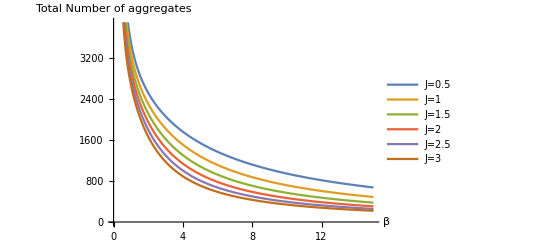

```mathematica
ListLinePlot[{(ⅇ^-J1+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J1×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J1+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J1×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))×10000,(ⅇ^-J105+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J105×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J105+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J105×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))×10000,(ⅇ^-J2+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J2×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J2+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J2×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))×10000,
(ⅇ^-J205+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J205×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J205+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J205×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))×10000,
(ⅇ^-J3+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J3×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J3+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J3×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))×10000,(ⅇ^-J305+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J305×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J305+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J305×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))×10000},DataRange->{0,15},PlotLegends->{"J=0.5","J=1","J=1.5","J=2","J=2.5","J=3","J=3.5"},AxesLabel->{"β","Total Number of aggregates"}]
```

General::munfl: Exp[-717.887] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-731.693] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-745.498] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

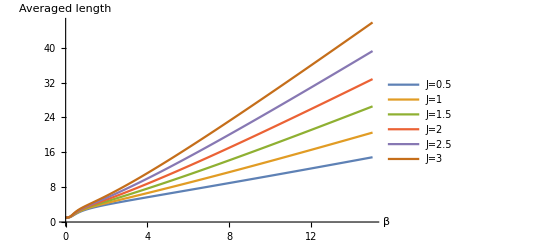

```mathematica
ListLinePlot[{(ⅇ^-J1+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J1×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J1+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J1×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)])),(ⅇ^-J105+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J105×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J105+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J105×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)])),(ⅇ^-J2+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J2×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J2+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J2×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)])),
(ⅇ^-J205+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J205×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J205+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J205×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)])),
(ⅇ^-J3+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J3×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J3+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J3×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)])),(ⅇ^-J305+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J305×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J305+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J305×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))},DataRange->{0,15},PlotLegends->{"J=0.5","J=1","J=1.5","J=2","J=2.5","J=3","J=3.5"},AxesLabel->{"β","Averaged length"}]
```